## Auxiliary functions

```mathematica
$HistoryLength = 10;

findEvolutionOperator2D[Ham_]:=(
funcs=Array[ψ[#2 + 8*(#1- 1)][t]&,{8, 2}];
equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[8][[{1, 2, 3, 4, 5,6 , 7, 8}, {1, 2}]]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]][[{1, 2}]]
)

fidelity2D[Mt_, Ma_] := (1/6)Sum[.25*Tr[Mt.(σI + σi).ConjugateTranspose[Mt].Ma.(σI + σi).ConjugateTranspose[Ma]], {σi, {σX, -σX, σY, -σY, σZ, -σZ}}];

fidelityXY[M_]:=(
Utarget = Cos[θ]*σX + Sin[θ]*σY;
NMaximize[Abs[fidelity2D[Utarget, M]], {θ}][[1]]
)

XYangle[M_] := (
Utarget = Cos[θ]*σX + Sin[θ]*σY;
θ /. NMaximize[Abs[fidelity2D[Utarget, M]], {θ}][[2]]
)

Clear[fidelityToGate];
fidelityToXYGate[Ea_?NumericQ, Ba_?NumericQ, ωEin_?NumericQ, ωBin_?NumericQ, Tmaxin_?NumericQ] := (
HcorrectedAtStart = Hcorrected;

Clear[Eamp, Bamp];
Eamp[t_] := Ea*cosWindow[t, Tmax/3, Tmax];
Bamp[t_] := Ba*cosWindow[t, Tmax/3, Tmax];
ωE = ωEin;
ωB = ωBin;
Tmax = Tmaxin;

U = findEvolutionOperator2D[Hcorrected, Tmax];
UU = U /. t->Tmax;

F = fidelityXY[UU] // Chop;

Print[{F, {ΔE, B0, Ea, Ba, ωEin, ωBin, Tmax}}];

output = F;

If[output > bestSoFar, (
bestSoFar = output;
bestParameters = {ΔE, B0, Ea, Ba, ωEin, ωBin, Tmax};
)];

Pause[1];

output
)

Clear[map]
map[x_, a_, b_] := a + (b - a)*x // Re
```

## Run optimization

```mathematica
setVariables[];

δ = 10^9;

EaD =116.68;
ωED = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 2*π*2.0548*10^8 /. ΔE->ΔEMid;
BaD = 0.015131;
ωBD = 2*π*(B0*γe - A*dState[[1]]^2/2) - 2*π*1.9759*10^8 /. ΔE->ΔEMid;

defaultEnergies = energiesInOrder[HexactStatic];
Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[defaultEnergies]];

Print["----------------------------------------" <> "startin'" <> "----------------------------------------"];
TimeConstrained[(
bestSoFar = 0;
bestParameters = {};

NMaximize[
{
fidelityToXYGate[
map[x1, EaD*.95, EaD*1.05],
 map[x1, BaD*.95, BaD*1.05],
map[x3, ωED - .05*10^9, ωED + .05*10^9],
map[x4, ωBD - .05*10^9, ωBD + .05*10^9],
100*10^-9],
0 < x1 < 1,
0 < x2 < 1,
0 < x3 < 1,
0 < x4 < 1(*,
0 < x5 < 1,
0<x6<1,
0<x7<1,
0<x8<1,
0<x9<1*)
},
{{x1,.3, .7}, {x2, .3, .7}, {x3, .3, .7}, {x4,.3, .7}(*, {x5,.3, .7}, {x6,.3, .7}, {x7,.3, .7}, {x8,.3, .7}, {x9,.3, .7}*)},
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]},
MaxIterations->10000
]

), 60*60*10
]

Do[(
Beep[];
Pause[.5];
), {i, 1, 10}]

clearVariables[]
```

----------------------------------------startin'----------------------------------------

{0.953592,{0,0.2,115.867,0.0150256,3.38815×10^10,3.37357×10^10,1/10000000}}

{0.98402,{0,0.2,117.844,0.0152819,3.38717×10^10,3.3706×10^10,1/10000000}}

{0.988154,{0,0.2,118.88,0.0154163,3.38823×10^10,3.37196×10^10,1/10000000}}

{0.979536,{0,0.2,117.43,0.0152283,3.38798×10^10,3.37133×10^10,1/10000000}}

{0.98715,{0,0.2,114.558,0.0148558,3.38811×10^10,3.37145×10^10,1/10000000}}

{0.818056,{0,0.2,118.489,0.0153656,3.3876×10^10,3.36911×10^10,1/10000000}}

{0.996236,{0,0.2,116.522,0.0151106,3.38801×10^10,3.37245×10^10,1/10000000}}

{0.999084,{0,0.2,116.472,0.015104,3.38778×10^10,3.37191×10^10,1/10000000}}

{0.994541,{0,0.2,115.993,0.0150419,3.38768×10^10,3.3722×10^10,1/10000000}}

{0.996998,{0,0.2,115.373,0.0149615,3.38889×10^10,3.37328×10^10,1/10000000}}

{0.981096,{0,0.2,119.066,0.0154404,3.38835×10^10,3.37335×10^10,1/10000000}}

{0.996313,{0,0.2,115.685,0.015002,3.38817×10^10,3.37193×10^10,1/10000000}}

{0.988272,{0,0.2,113.146,0.0146727,3.38819×10^10,3.37282×10^10,1/10000000}}

{0.996277,{0,0.2,114.579,0.0148586,3.3882×10^10,3.37261×10^10,1/10000000}}

{0.999141,{0,0.2,114.532,0.0148525,3.38851×10^10,3.37241×10^10,1/10000000}}

{0.99597,{0,0.2,113.537,0.0147234,3.38877×10^10,3.37239×10^10,1/10000000}}

{0.992679,{0,0.2,116.451,0.0151014,3.38848×10^10,3.37216×10^10,1/10000000}}

{0.998989,{0,0.2,115.047,0.0149193,3.38827×10^10,3.37249×10^10,1/10000000}}

{0.993271,{0,0.2,115.027,0.0149167,3.38856×10^10,3.37312×10^10,1/10000000}}

{0.998945,{0,0.2,115.521,0.0149806,3.38827×10^10,3.37222×10^10,1/10000000}}

{0.996681,{0,0.2,115.413,0.0149667,3.38752×10^10,3.37123×10^10,1/10000000}}

{0.998909,{0,0.2,115.383,0.0149628,3.38855×10^10,3.37277×10^10,1/10000000}}

{0.998748,{0,0.2,115.403,0.0149654,3.38787×10^10,3.37175×10^10,1/10000000}}

{0.999367,{0,0.2,115.388,0.0149635,3.38838×10^10,3.37251×10^10,1/10000000}}

{0.99891,{0,0.2,115.199,0.014939,3.38821×10^10,3.37244×10^10,1/10000000}}

{0.999376,{0,0.2,115.44,0.0149702,3.38825×10^10,3.37228×10^10,1/10000000}}

{0.997741,{0,0.2,115.869,0.0150258,3.38819×10^10,3.37206×10^10,1/10000000}}

{0.999473,{0,0.2,115.253,0.0149459,3.38825×10^10,3.37239×10^10,1/10000000}}

{0.999776,{0,0.2,113.834,0.014762,3.38892×10^10,3.37289×10^10,1/10000000}}

{0.999746,{0,0.2,112.516,0.014591,3.38949×10^10,3.37338×10^10,1/10000000}}

{0.998815,{0,0.2,115.426,0.0149683,3.38839×10^10,3.37262×10^10,1/10000000}}

{0.999534,{0,0.2,114.755,0.0148814,3.38848×10^10,3.37246×10^10,1/10000000}}

{0.999483,{0,0.2,114.254,0.0148163,3.38857×10^10,3.37249×10^10,1/10000000}}

{0.999896,{0,0.2,113.608,0.0147326,3.38886×10^10,3.37284×10^10,1/10000000}}

{0.999965,{0,0.2,112.692,0.0146138,3.38916×10^10,3.37312×10^10,1/10000000}}

{0.998897,{0,0.2,112.515,0.0145909,3.38932×10^10,3.37309×10^10,1/10000000}}

{0.999759,{0,0.2,114.568,0.0148572,3.38852×10^10,3.37256×10^10,1/10000000}}

{0.999881,{0,0.2,113.672,0.0147409,3.38897×10^10,3.37302×10^10,1/10000000}}

{0.999936,{0,0.2,112.628,0.0146055,3.3893×10^10,3.37333×10^10,1/10000000}}

{0.999956,{0,0.2,111.844,0.0145039,3.38966×10^10,3.37362×10^10,1/10000000}}

{0.999728,{0,0.2,111.583,0.01447,3.38963×10^10,3.37365×10^10,1/10000000}}

{0.999939,{0,0.2,113.272,0.014689,3.3891×10^10,3.37308×10^10,1/10000000}}

{0.999864,{0,0.2,111.546,0.0144652,3.38964×10^10,3.37355×10^10,1/10000000}}

{0.999963,{0,0.2,113.14,0.014672,3.38914×10^10,3.37315×10^10,1/10000000}}

{0.999865,{0,0.2,112.846,0.0146339,3.38923×10^10,3.37315×10^10,1/10000000}}

{0.999981,{0,0.2,112.682,0.0146126,3.38928×10^10,3.37329×10^10,1/10000000}}

$Aborted

$Aborted

## Test X-gate

0.996694

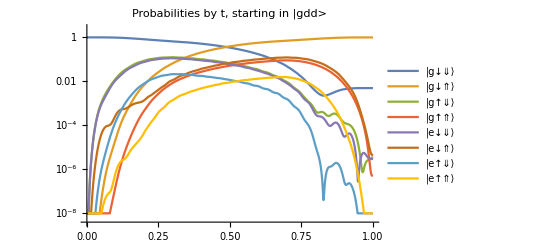

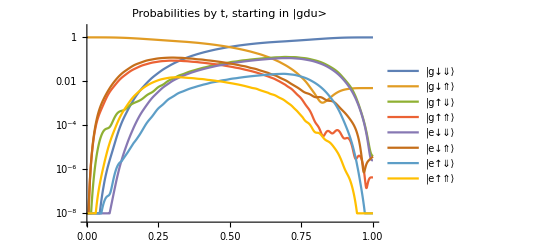

```mathematica
(*Vt = γe*B0 + γn*B0; (* Hz *)
ΔE = 0;
Δγ = 0;
HexactStatic[[6, 6]] - HexactStatic[[3, 3]] // FullSimplify*)

setVariables[]
ΔE = 0;

Tmax = 100*10^-9;

Clear[Eamp, Bamp];
Ea =116.68;
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 2*π*2.0548*10^8 /. ΔE->ΔEMid;
Eamp[t_] := EaD*cosWindow[t, Tmax/3, Tmax];
Ba = 0.015131;
ωB = 2*π*(B0*γe - A*dState[[1]]^2/2) - 2*π*1.9759*10^8 /. ΔE->ΔEMid;
Bamp[t_] := BaD*cosWindow[t, Tmax/3, Tmax];

U = findEvolutionOperator2D[Hcorrected, Tmax];
UU = U /. t->Tmax;

F = fidelityXY[UU] // Chop;
Print[F]

Evaluate@Table[Max[Abs[Uuncut[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]

(*Fs = {};
ΔEs = Table[e + ΔE, {e, -600, 600, 20}];

Do[
(
ΔE = deltaE;
Uax = ConjugateTranspose[Ubase].ConjugateTranspose[Urot].findEvolutionOperator[Hcorrected];

U = Uax/. t->Tmax;

F = fidelity2D[targetGate, U[[{1, 2}, {1, 2}]]] // Chop;

AppendTo[Fs, {ΔE, F}];

Pause[.5];

Print[{ΔE, F}];
),

{deltaE, ΔEs}
]

ListPlot[Fs, AxesLabel->{"ΔE", "F"}]*)

clearVariables[]
```

```mathematica
FsX = Fs;
```

```mathematica
FsY2 = Fs;
```

RandomVariate::posprm: Parameter σ at position 2 in NormalDistribution[0,σ] is expected to be positive.

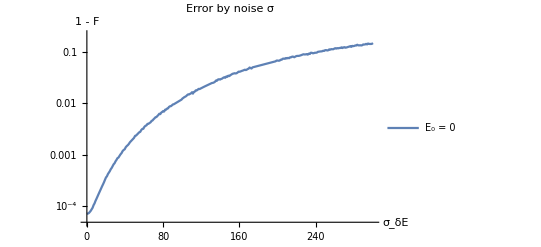

```mathematica
Clear[FgivenSD]
FgivenSD[σ_, μ_, Fint_] := (
Mean[Fint[RandomVariate[NormalDistribution[μ, σ], 10000]]]
)

fidelityData = {{FsX, 0, "E_0 = 0"}} // Transpose;

fidelityPoints = fidelityData[[1]];
means = fidelityData[[2]];
names = fidelityData[[3]];

Fints = Map[Interpolation, fidelityPoints];

LogPlot[Evaluate@Table[1 - FgivenSD[σ, means[[i]], Fints[[i]]], {i, Length[names]}], {σ, .0001, 300}, AxesLabel->{Subscript[σ, δE], "1 - F"}, PlotLegends->names, PlotLabel->"Error by noise σ", PlotPoints->10, MaxRecursion->5]
```